```mathematica
Quit[]
```

```mathematica
NotebookEvaluate[EvaluationNotebook[],EvaluationElements->"InitializationCell"];
```

```mathematica
SetDirectory@NotebookDirectory[];
Off[Part::partd,Part::pspec1,Message::name];
```

```mathematica
Clear["Global`*"];
```

## Pre - load

```mathematica
SetDirectory[NotebookDirectory[]];
NormalVector=Normalize@Cross[#⟦2⟧-#⟦1⟧,#⟦3⟧-#⟦1⟧]&;
NodesElements={MeshCoordinates@#, Reverse/@MeshCells[#,2]⟦All,1⟧}&;
ExportModelCSV[name_,nodes_,elements_]:=
Export[name<>".csv",StringJoin@@Riffle[Join[{ToString@Length@nodes<>","<>ToString@Length@elements,ExportString[nodes,"CSV"]},Flatten[{ToString@Length@#,ExportString[#,"CSV"]}&/@((Reverse/@#)&/@elements),1]],"\n"],"Text"];
Nodes=<||>;
Elements=<||>;
Triangles=<||>;
ImportModelSTL[name_]:=Module[{path=FileNameJoin@{"Model",name,name},model,nodes,elements},
model=ConnectedMeshComponents@Import[path<>".stl"];
{nodes,elements}=(NodesElements/@model)ᵀ;
elements+=Prepend[Accumulate@Most[Length/@nodes],0];
nodes=Join@@nodes;
Nodes[name]=nodes;
Elements[name]=elements;
Triangles[name]=(nodes⟦#⟧&/@(Join@@elements)⟦All,1;;3⟧);
ExportModelCSV[path,nodes,elements];
Table[Show[model,HighlightMesh[model⟦i⟧,Style[1,Red]],ImageSize->30],{i,Length@model}]
];
```

### LuaLink

```mathematica
Install[(*"cmd /k "<>*)FileNameJoin@{NotebookDirectory[],"Lua","luajit.exe "}<>FileNameJoin@{NotebookDirectory[],"Lua","LuaLink.lua"}];
LuaFunctionCast[name_String]:=Lua["function(...)return "<>name<>"(...)end"];
```

```mathematica
Lua["ffi = require('ffi')
local file = io.open([["<>FileNameJoin@{NotebookDirectory[],"BEM","BEM.lua.h"}<>"]])
bem = ffi.load('BEM')
ffi.cdef(file:read('*all'))
file:close()"]
```

```mathematica
BemNewWorld=LuaFunctionCast["bem.new_world"];
BemLoadCsv=LuaFunctionCast["bem.load_csv"];
BemSolve=LuaFunctionCast["bem.solve"];
BemRegion=LuaFunctionCast["bem.region"];
BemPoint=LuaFunctionCast["bem.point"];
BemDelWorld=LuaFunctionCast["bem.del_world"];
If[ValueQ@BemWorld,BemDelWorld/@Values[BemWorld]];
BemWorld=<||>;
```

#### Uninstall

```mathematica
Uninstall@Last@Links["*LuaLink.lua*"];
LinkClose/@Links["*LuaLink.lua*"];
```

### MATLink

```mathematica
Needs@"MATLink`";
(*SetOptions[MATLink,"Force32BitEngine"->True]*)
OpenMATLAB[]
```

```mathematica
permute=MFunction["permute"];
MEvaluate["cd '"<>FileNameJoin@{NotebookDirectory[],"MATLAB'"}];
MIntGreen=MFunction["int_green3d_tri","OutputArguments"->2];
MCharge=MFunction["Charge"];
MPotential=MFunction["Potential","OutputArguments"->4];
```

#### Install

copy MATLink folder to $UserBaseDirectory/Applications
add C:\Program Files\MATLAB\R2015b\bin\win64\libmx.dll to PATH

```mathematica
SystemOpen@$UserBaseDirectory;
```

## Calculate Method

```mathematica
Options[ChargeBasis]={Method->MATLAB};
ChargeBasis[name_String,opts:OptionsPattern[]]:=Module[
{path,func=OptionValue[opts,Method],charges},
path=FileNameJoin@{"Model",name,name<>"-charge-"<>ToString@func<>".mat"};
If[FileExistsQ[path],
charges=Import[path]⟦1⟧,
charges=ChargeBasisMethod[func][FileNameJoin@{"Model",name,name}];
Export[path,charges]
];
charges
];
ChargeBasisMethod[MATLAB][path_String]:=(MCharge[FileNameJoin@{"..",path}]ᵀ);
ChargeBasisMethod[BEM][path_String]:= Module[
{name=FileBaseName@path,wr,data,pos,n,amountOfElectrodes,tol,maxit,numMom,numLev,checksum},
wr=BemNewWorld[path,0.001,64,6,6,1,1000];
BemWorld[name]=wr;
BemLoadCsv[wr,path<>".csv",44];
BemSolve[wr];
data=Import[path,"Byte"];
pos=Prepend[Flatten@Position[data,10,1,7],0];
{n,amountOfElectrodes,tol,maxit,numMom,numLev,checksum}=Read[StringToStream@FromCharacterCode@data⟦#⟧,Number]&/@(Span@@(#+{1,-1})&/@Partition[pos,2,1]);
4π Partition[ImportString[FromCharacterCode@data⟦Last@pos+1;;-1⟧,"Real64"],n]
];
ChargeBasisMethod[CHIBE][path_String]:=Module[
{name=FileBaseName@path,elements,charges,values},
SetDirectory@"CHIBE";
Export["nodes.csv",Nodes@name];
elements=Elements@name;
charges=Table[
values=Join@@Table[Join[#,{1,KroneckerDelta[k,i]}]&/@elements⟦i⟧,{i,Length@elements}];
Export["elements.csv",values];
Run[FileNameJoin@{"..","Lua","luajit"}<>" preCHIBE.lua "<>name];
Run["3D_Potential_CHBIE_FMM_64"];
values=Rest/@Import["output.dat","Table"]⟦3;;-1⟧;
values⟦All,2⟧
,{k,Length@elements}];
SetDirectory@"..";
charges
];

Options[PotentialBasis]={Method->MATLAB};
PotentialBasis[name_String,{x0_,x1_,dx_},{y0_,y1_,dy_},{z0_,z1_,dz_},opts:OptionsPattern[]]:=Module[
{path,func=OptionValue[opts,Method],potential},
path=FileNameJoin@{"Model",name,name<>"-potential-"<>ToString@func<>".mat"};
If[FileExistsQ[path],
potential=Import[path],
potential=PotentialBasisMethod[func][FileNameJoin@{"Model",name,name},{x0,x1,dx},{y0,y1,dy},{z0,z1,dz}];
Export[path,potential]
];
potential
];
PotentialBasisMethod[MATLAB][path_String,{x0_,x1_,dx_},{y0_,y1_,dy_},{z0_,z1_,dz_}]:=Module[
{name=FileBaseName@path,charges,triangles,points},
charges=ChargeBasis[name,Method->MATLAB];
triangles=permute[Triangles@name,{2,3,1}];
points=Flatten[Table[{x,y,z},{x,x0,x1,dx},{y,y0,y1,dy},{z,z0,z1,dz}],2];
Re@MPotential[triangles,#.charges ,points]&/@IdentityMatrix@Length@Elements@name
];
PotentialBasisMethod[BEM][path_String,{x0_,x1_,dx_},{y0_,y1_,dy_},{z0_,z1_,dz_}]:=Module[
{name=FileBaseName@path,wr,data,pos,n,amountOfElectrodes,tol,maxit,numMom,numLev,checksum,xmin,xmax,nx,ymin,ymax,ny,zmin,zmax,nz},
nx=Floor[(x1-x0)/dx]+1;
ny=Floor[(y1-y0)/dy]+1;
nz=Floor[(z1-z0)/dz]+1;
wr=BemWorld@name;
If[Head@wr=!=LuaObject,BemWorld[name]=wr=BemNewWorld[path,0.001,64,6,6,1,1000]];
BemLoadCsv[wr,path<>".csv",44];
BemRegion[wr,x0,x1,nx,y0,y1,ny,z0,z1,nz];
data=Import[path<>"calc","Byte"];
pos=Prepend[Flatten@Position[data,10,1,16],0];
{n,amountOfElectrodes,tol,maxit,numMom,numLev,checksum,xmin,xmax,nx,ymin,ymax,ny,zmin,zmax,nz}=Read[StringToStream@FromCharacterCode@data⟦#⟧,Number]&/@(Span@@(#+{1,-1})&/@Partition[pos,2,1]);
({1,-1,-1,-1}(Partition[#,nx*ny*nz]&/@Partition[ImportString[FromCharacterCode@data⟦Last@pos+1;;-1⟧,"Real64"],nx*ny*nz*amountOfElectrodes]))ᵀ
];
```

## sphere

```mathematica
ImportModelSTL@"sphere"
```

{-Graphics3D-}

```mathematica
cb1=ChargeBasis["sphere",Method->MATLAB];
```

```mathematica
cb2=ChargeBasis["sphere",Method->BEM];
```

```mathematica
cb3=ChargeBasis["sphere",Method->CHIBE];
```

```mathematica
Abs[cb1-cb2]//Max
```

0.0685407

```mathematica
Abs[cb2-cb3]//Max
```

0.106325

```mathematica
pb1=PotentialBasis["sphere",{-2,2,0.1},{-2,2,0.1},{0,0,1},Method->MATLAB];
```

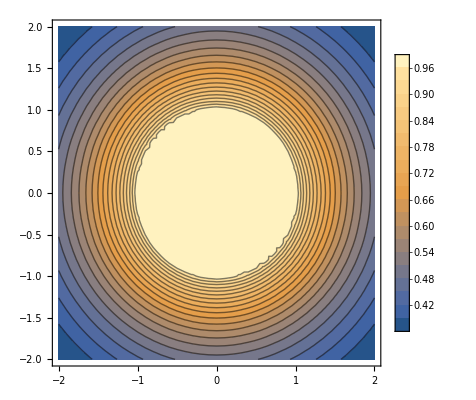

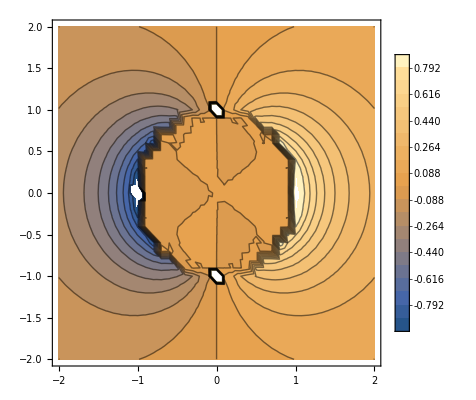

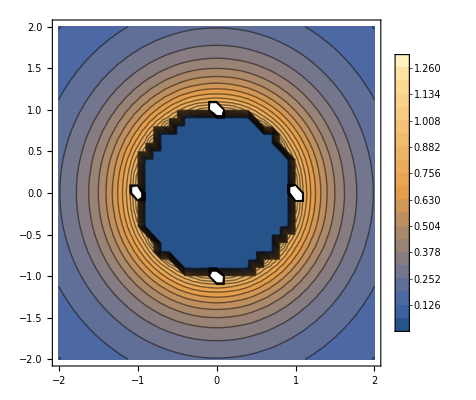

```mathematica
{pot,fx,fy,fz}={1}.pb1;
ListContourPlot[Flatten/@({N@Tuples[{Range[-2,2,0.1],Range[-2,2,0.1]}],pot}ᵀ),Contours->20,PlotLegends->Automatic]
ListContourPlot[Flatten/@({N@Tuples[{Range[-2,2,0.1],Range[-2,2,0.1]}],fx}ᵀ),Contours->20,PlotLegends->Automatic]
ListContourPlot[Flatten/@({N@Tuples[{Range[-2,2,0.1],Range[-2,2,0.1]}],√(fx^2+fy^2+fz^2)}ᵀ),Contours->20,PlotLegends->Automatic]
```

```mathematica
pb2=PotentialBasis["sphere",{-2,2,0.1},{-2,2,0.1},{0,0,1},Method->BEM];
```

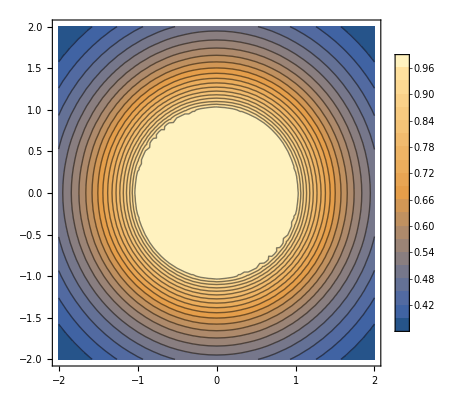

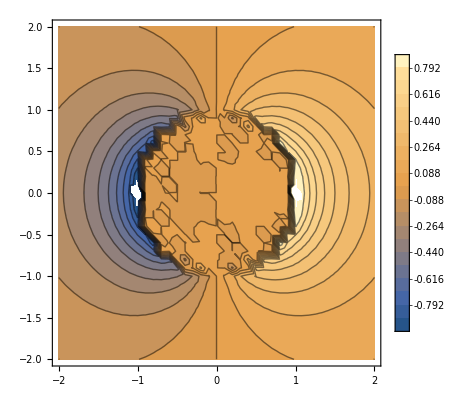

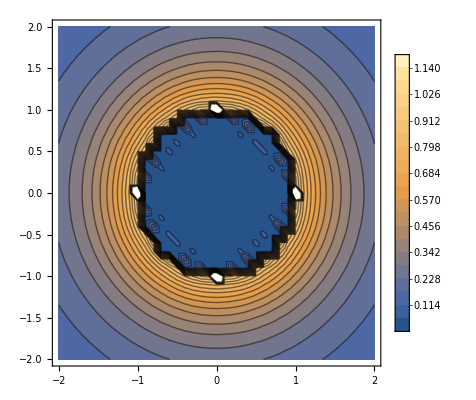

```mathematica
{pot,fx,fy,fz}={1}.pb2;
ListContourPlot[Flatten/@({N@Tuples[{Range[-2,2,0.1],Range[-2,2,0.1]}],pot}ᵀ),Contours->20,PlotLegends->Automatic]
ListContourPlot[Flatten/@({N@Tuples[{Range[-2,2,0.1],Range[-2,2,0.1]}],fx}ᵀ),Contours->20,PlotLegends->Automatic]
ListContourPlot[Flatten/@({N@Tuples[{Range[-2,2,0.1],Range[-2,2,0.1]}],√(fx^2+fy^2+fz^2)}ᵀ),Contours->20,PlotLegends->Automatic]
```

## 4rod

```mathematica
ImportModelSTL@"4rod"
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
cb1=ChargeBasis["4rod",Method->MATLAB];
```

```mathematica
cb2=ChargeBasis["4rod",Method->BEM];
```

```mathematica
cb3=ChargeBasis["4rod",Method->CHIBE];
```

```mathematica
Abs[cb1-cb2]//Max
```

0.280908

```mathematica
Abs[cb2-cb3]//Max
```

282.51

```mathematica
pb1=PotentialBasis["4rod",{-0.04,0.04,0.001},{-0.04,0.04,0.001},{2.1,2.1,1},Method->MATLAB];
```

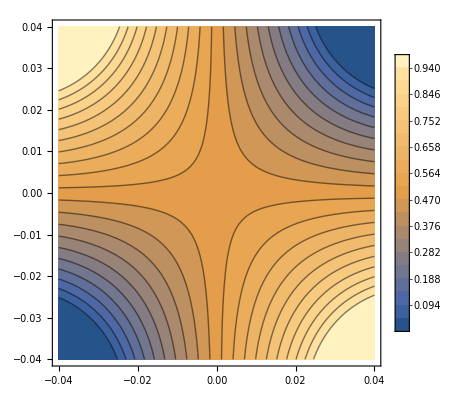

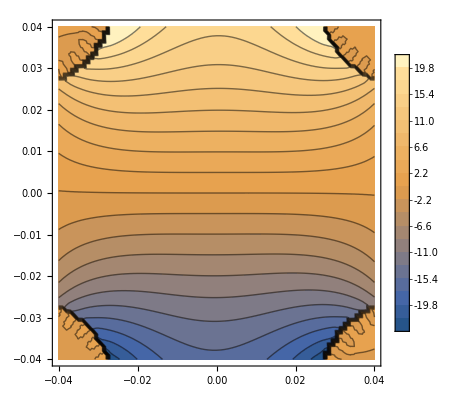

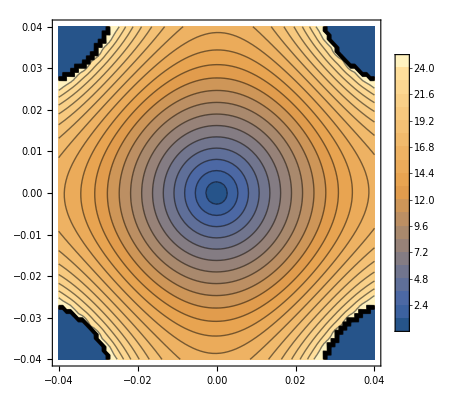

```mathematica
{pot,fx,fy,fz}={0,1,0,1,0,0}.pb1;
ListContourPlot[Flatten/@({N@Tuples[{Range[-0.04,0.04,0.001],Range[-0.04,0.04,0.001]}],pot}ᵀ),Contours->20,PlotLegends->Automatic]
ListContourPlot[Flatten/@({N@Tuples[{Range[-0.04,0.04,0.001],Range[-0.04,0.04,0.001]}],fx}ᵀ),Contours->20,PlotLegends->Automatic]
ListContourPlot[Flatten/@({N@Tuples[{Range[-0.04,0.04,0.001],Range[-0.04,0.04,0.001]}],√(fx^2+fy^2+fz^2)}ᵀ),Contours->20,PlotLegends->Automatic]
```

```mathematica
pb2=PotentialBasis["4rod",{-0.04,0.04,0.001},{-0.04,0.04,0.001},{2.1,2.1,1},Method->BEM];
```

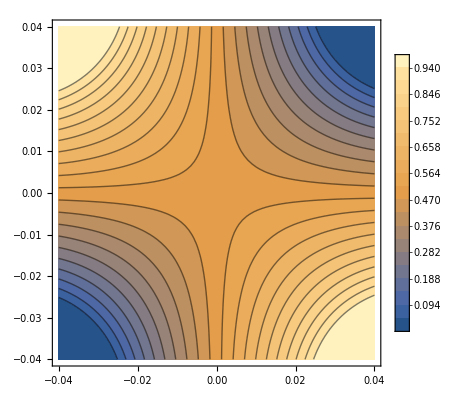

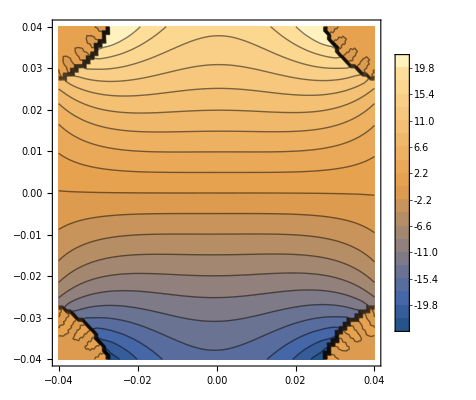

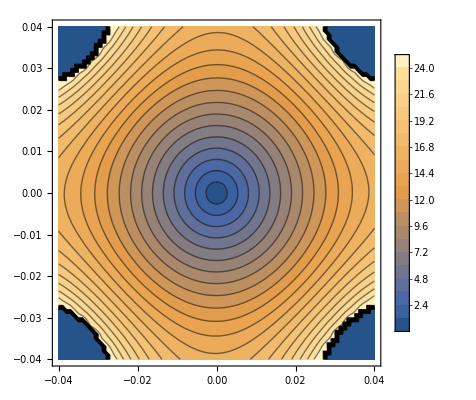

```mathematica
{pot,fx,fy,fz}={0,1,0,1,0,0}.pb2;
ListContourPlot[Flatten/@({N@Tuples[{Range[-0.04,0.04,0.001],Range[-0.04,0.04,0.001]}],pot}ᵀ),Contours->20,PlotLegends->Automatic]
ListContourPlot[Flatten/@({N@Tuples[{Range[-0.04,0.04,0.001],Range[-0.04,0.04,0.001]}],fx}ᵀ),Contours->20,PlotLegends->Automatic]
ListContourPlot[Flatten/@({N@Tuples[{Range[-0.04,0.04,0.001],Range[-0.04,0.04,0.001]}],√(fx^2+fy^2+fz^2)}ᵀ),Contours->20,PlotLegends->Automatic]
```